```mathematica
Needs["PiCbench`"]
```

## 1- Parameter definition

Check the default parameter set

```mathematica
MagnitudeList[]
```

Variable | Value | Description
dx | 1 | Length of cell size in the x dimension
nx | 1024 | Number of cells
qp | 0.0004 | Charge of a macroparticle (absolute value)
mp | 0.0004 | Mass of electron macroparticle
np | 3000 | Number of particles
ionMass | 1836.15 | Relative mass of ion species/mass of electrons
dt | 1 | Temporal step
a | 1 | Charge dimenssion in the Maxwell equations
b | 1 | Relative dimension of the magnetic field in the maxwell equations
c | 1 | Speed of light
charSpeed | 0.5 | A characteristic speed of the electrons in the plasma.
charSpeedIons | 0.0116685 | Ion characteristic speed (derived magnitude)
lx | 1024 | System length (derived magnitude)
wp | 0.0342327 | Plasma frecuency (derived magnitude)
debyeLength | 14.6059 | Debye length (derived magnitude)

```mathematica
PrintConditions[]
```

Small cell condition - (dx<<lx) - 1 << 1024

Small time-step condition - (dt<<wp^-1) - 1 << 29.2119

Big world condition - (debyeLength<<lx) - 14.6059 << 1024

Change a certain parameter

```mathematica
PicPar["charSpeed"]=10;
```

```mathematica
PrintConditions[]
```

Small cell condition - (dx<<lx) - 1 << 1024

Small time-step condition - (dt<<wp^-1) - 1 << 29.2119

Big world condition - (debyeLength<<lx) - 292.119 << 1024

```mathematica
PicPar["charSpeed"]=0.5;
```

If intereseted in using different sets in the same notebook/script consider:

```mathematica
CreatePicPar[PicParDemo];
PicParDemo["np"]=10;
```

```mathematica
MagnitudeList[PicParDemo]
PrintConditions[PicParDemo]
```

Variable | Value | Description
dx | 1 | Length of cell size in the x dimension
nx | 1024 | Number of cells
qp | 0.0004 | Charge of a macroparticle (absolute value)
mp | 0.0004 | Mass of electron macroparticle
np | 10 | Number of particles
ionMass | 1836.15 | Relative mass of ion species/mass of electrons
dt | 1 | Temporal step
a | 1 | Charge dimenssion in the Maxwell equations
b | 1 | Relative dimension of the magnetic field in the maxwell equations
c | 1 | Speed of light
charSpeed | 0.5 | A characteristic speed of the electrons in the plasma.
charSpeedIons | 0.0116685 | Ion characteristic speed (derived magnitude)
lx | 1024 | System length (derived magnitude)
wp | 0.00197642 | Plasma frecuency (derived magnitude)
debyeLength | 252.982 | Debye length (derived magnitude)

Small cell condition - (dx<<lx) - 1 << 1024

Small time-step condition - (dt<<wp^-1) - 1 << 505.964

Big world condition - (debyeLength<<lx) - 252.982 << 1024

## 2- Initialization

```mathematica
?UniformParticles1D
```

UniformParticles1D[vMax] generates a uniform particle distribution in [0, lx] x [-vMax,vMax].
By default vMax is 2 times the charSpeed parameter.

```mathematica
UniformParticles1D[PicParameters->PicParDemo]
```

{{7.21002,0.0223178},{980.991,0.948542},{748.18,-0.438051},{674.025,0.141101},{44.0577,0.527865},{992.111,-0.439892},{557.789,-0.504293},{264.14,-0.393985},{979.,0.646194},{1013.13,0.325557}}

```mathematica
UniformParticles1D[0.01,PicParameters->PicParDemo]
```

{{417.999,-0.00420934},{498.937,-0.00938955},{724.169,-0.00486444},{961.464,0.00706034},{597.635,-0.00182192},{267.43,0.00514825},{341.273,-0.00698584},{110.264,-0.00715644},{61.8551,0.00530715},{401.699,-0.00506974}}

```mathematica
electrons=UniformParticles1D[];
```

```mathematica
ions=UniformParticles1D[UseIonDefaults->True];
```

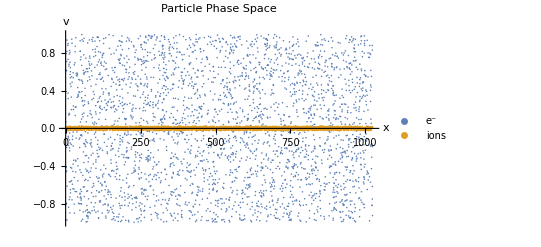

```mathematica
PhaseSpacePlot[{electrons,ions},PlotLegends->{"e^-","ions"}]
```

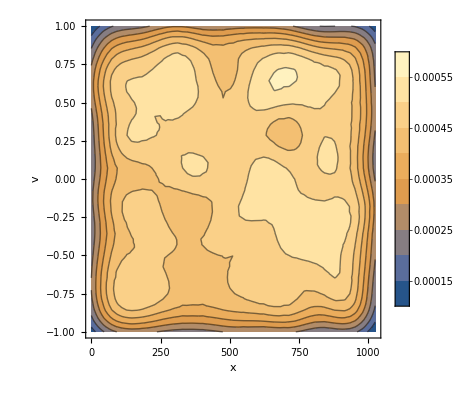

```mathematica
SmoothPhaseSpacePlot[electrons,PlotLegends->Automatic]
```

See initial distributions available

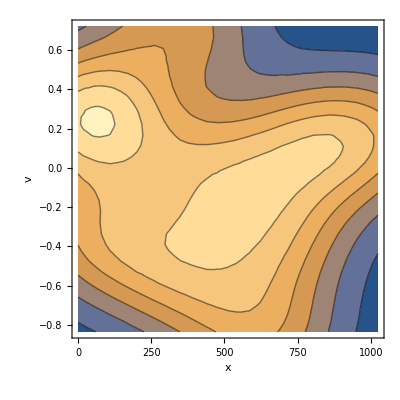
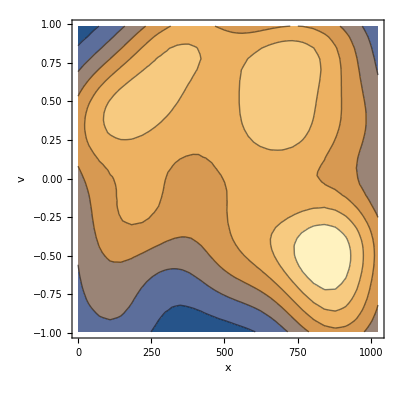
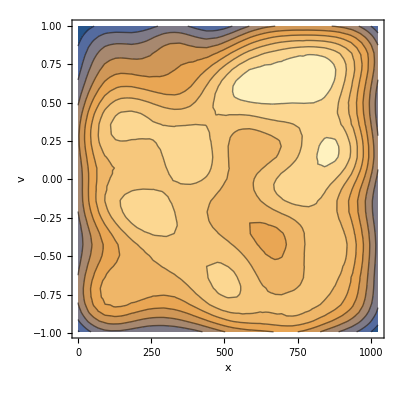
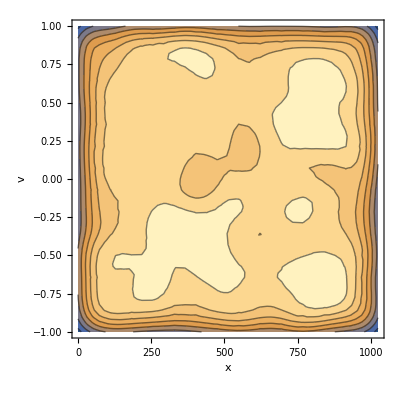
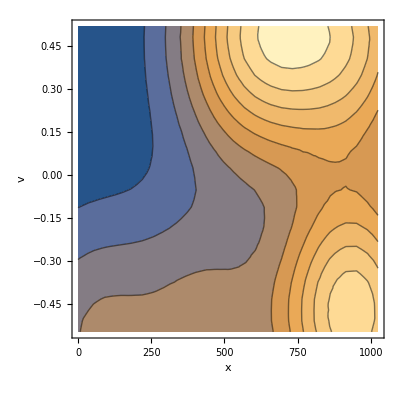
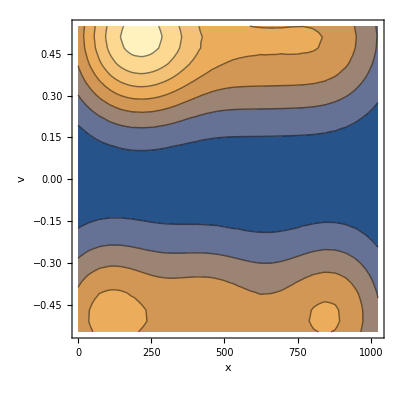
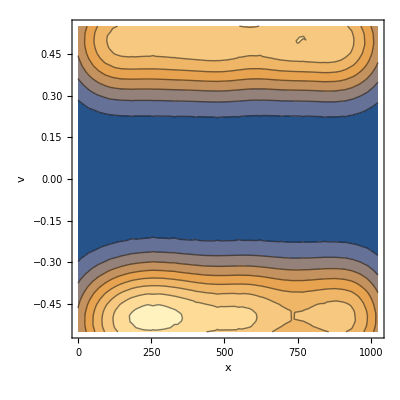
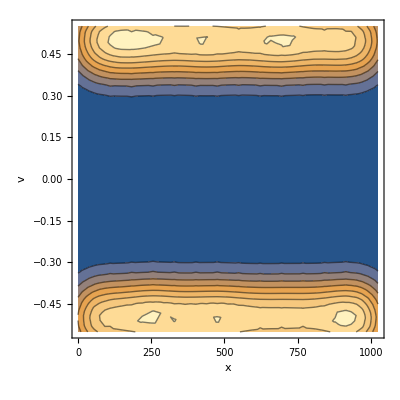
| 10 | 100 | 1000 | 10000
UniformParticles1D | -Graphics- | -Graphics- | -Graphics- | -Graphics-
CounterDriftParticles1D | -Graphics- | -Graphics- | -Graphics- | -Graphics-
GaussianParticles1D | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[PicParDemo["np"]=i;SmoothPhaseSpacePlot[f[PicParameters->PicParDemo]],{f,{UniformParticles1D,CounterDriftParticles1D,GaussianParticles1D}},{i,{10,100,1000,10000}}],TableHeadings->{{UniformParticles1D,CounterDriftParticles1D,GaussianParticles1D},{10,100,1000,10000}}]
```

## 3- Particle to grid

```mathematica
?GetRho1D
```

GetRho1D[] returns a functions that calculates rho(particleList).
Relevant parameters are dx,nx,qc.
Can also be used with qc=1 to find number density.

A trick to see the code in a cleaned style:

```mathematica
Begin["PiCbench`Particle2Grid`Private`"];
Quiet[GetRho1D[PicParameters->Symbol,Method->"First-order"],{Table::iterb}]
End[];
```

Function[{particles},Block[{rho,pos,x,PiCbench`Particle2Grid`Private`i},rho=Table[0.,{1+nx}];For[PiCbench`Particle2Grid`Private`i=1,PiCbench`Particle2Grid`Private`i≤Length[particles],PiCbench`Particle2Grid`Private`i++,x=particles⟦PiCbench`Particle2Grid`Private`i,1⟧;pos=Floor[x];rho⟦pos+1⟧+=pos+1-x;rho⟦pos+2⟧+=x-pos;];rho⟦1⟧+=rho⟦nx+1⟧;(Drop[rho,-1] qp)/dx]]

Use should be made by using a compiled function

```mathematica
getρ=FCompile[GetRho1D[],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

Automatic benchmark of compilation:

```mathematica
TableForm[{BenchmarkFCompile[{GetRho1D[],{_Real},{2}},{electrons},100],BenchmarkFCompile[{GetRho1D[Method->"Zeroth-order"],{_Real},{2}},{electrons},100]},TableHeadings->{{"1st","0th"},{"None","WVM","C","CSpeed"}}]
```

| None | WVM | C | CSpeed
1st | 0.0224963 | 0.00073177 | 0.00017824 | 0.00005249
0th | 0.0123371 | 0.00023305 | 0.0001252 | 0.00005742

```mathematica
ρElectron=getρ[electrons];
```

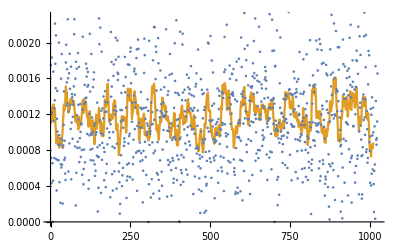

```mathematica
ListPlot[{ρElectron,DebyeMovingAverage[ρElectron]},Joined->{False,True}]
```

```mathematica
ρIon=getρ[ions];
```

## 4- Solving Maxwell

```mathematica
getE=FCompile[GetE1D[],{_Real},{1},{{Re[__],_Real,1}},CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
eField=getE[(ρIon-ρElectron)];
```

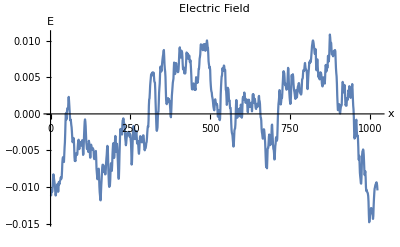

```mathematica
ListPlot[{eField},PlotLabel->"Electric Field",AxesLabel->{"x","E"},Joined->True]
```

The efficiency of Fourier methods rely on using FFT techniques.
Test speed using two configurations, one allowing for FFT

```mathematica
CreatePicPar[Demo1];Demo1["nx"]=1000;
CreatePicPar[Demo2];Demo2["nx"]=1024;
```

```mathematica
Demo1getρ=FCompile[GetRho1D[PicParameters->Demo1],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"];
Demo2getρ=FCompile[GetRho1D[PicParameters->Demo2],{_Real},{2},CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
Demo1e=Demo1getρ[UniformParticles1D[PicParameters->Demo1]];
Demo1i=Demo1getρ[UniformParticles1D[PicParameters->Demo1,UseIonDefaults->True]];
Demo2e=Demo2getρ[UniformParticles1D[PicParameters->Demo2]];
Demo2i=Demo2getρ[UniformParticles1D[PicParameters->Demo2,UseIonDefaults->True]];
```

```mathematica
{BenchmarkFCompile[{GetE1D[PicParameters->Demo1,Method->"Fourier"],{_Real},{1},{{Re[__],_Real,1}}},{Demo1i-Demo1e},2000],
BenchmarkFCompile[{GetE1D[PicParameters->Demo2,Method->"Fourier"],{_Real},{1},{{Re[__],_Real,1}}},{Demo2i-Demo2e},2000],
BenchmarkFCompile[{GetE1D[PicParameters->Demo1,Method->"Fourier-diff"],{_Real},{1},{{Re[__],_Real,1}}},{Demo1i-Demo1e},2000],BenchmarkFCompile[{GetE1D[PicParameters->Demo2,Method->"Fourier-diff"],{_Real},{1},{{Re[__],_Real,1}}},{Demo2i-Demo2e},2000]}//TableForm[#,TableHeadings->{{"1000 - Fourier","1024 - Fourier","1000 - Fourier-diff","1024 - Fourier-diff"},{"None","WVM","C","CSpeed"}}]&
```

| None | WVM | C | CSpeed
1000 - Fourier | 0.000399535 | 0.0000954925 | 0.0000882845 | 0.000088047
1024 - Fourier | 0.000340581 | 0.000059149 | 0.000060519 | 0.000057448
1000 - Fourier-diff | 0.000278783 | 0.000107755 | 0.000106757 | 0.000105905
1024 - Fourier-diff | 0.000275352 | 0.0000789765 | 0.000078565 | 0.0000797205

## 5- Particle Mover

```mathematica
stepElectrons=FCompile[StepParticles1DES[-1],{_Real,_Real},{1,2},CompilationTarget->"C",RuntimeOptions->"Speed"];
stepIons=FCompile[StepParticles1DES[1/PicPar["ionMass"]],{_Real,_Real},{1,2},CompilationTarget->"C",RuntimeOptions->"Speed"];
```

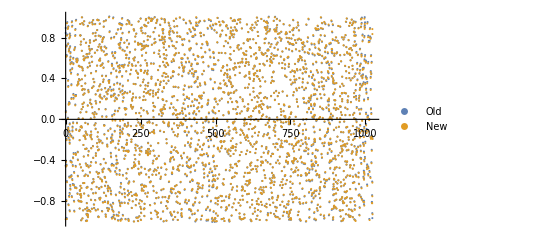

```mathematica
ListPlot[{stepElectrons[eField,electrons],electrons},PlotLegends->{"Old","New"}]
```

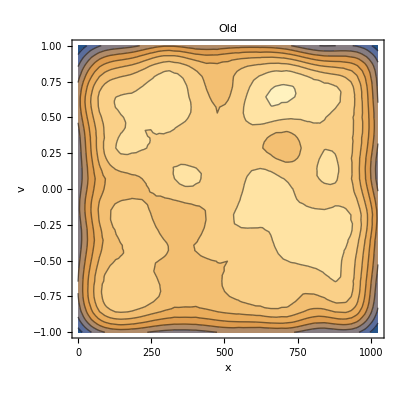
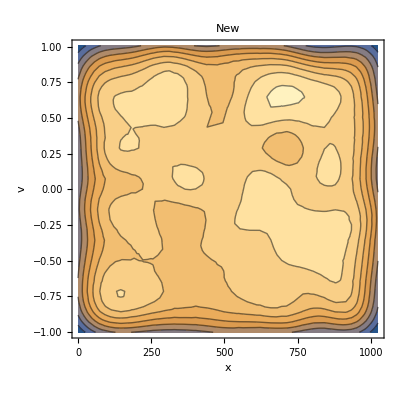

```mathematica
{SmoothPhaseSpacePlot[electrons,PlotLabel->"Old"],SmoothPhaseSpacePlot[stepElectrons[eField,electrons],PlotLabel->"New"]}
```

## 6- A full simulation cycle

```mathematica
electrons=UniformParticles1D[];
ions=UniformParticles1D[UseIonDefaults->True];
nSubsteps=3;(*Steps in time Δt done before saving data for diagnostics*)
nSteps=30;(*Number of cycles repeating the previous*)
```

```mathematica
eFieldList=Table[0,{nSteps}];
ρElectronList=Table[0,{nSteps}];
ρIonList=Table[0,{nSteps}];
electronsList=Table[0,{nSteps}];
ionsList=Table[0,{nSteps}];
AbsoluteTiming[Do[
Do[ (*PiC cycle:*)
(*Particle to grid*)
ρElectron=getρ[electrons];ρIon=getρ[ions];
(*Solve Maxwell*)
eField=getE[(ρIon-ρElectron)];
(*Move particles (includes field interpolation)*)
electrons=stepElectrons[eField,electrons];ions=stepIons[eField,ions];
,{nSubsteps}];
(*Save data*)
eFieldList[[i]]=eField;
ρElectronList[[i]]=ρElectron;
ρIonList[[i]]=ρIon;
electronsList[[i]]=electrons;
ionsList[[i]]=ions;,{i,nSteps}];]
```

{0.065272,Null}

## 7- Diagnostics

```mathematica
Manipulate[ListPlot[{DebyeMovingAverage[ρElectronList[[i]]],DebyeMovingAverage[ρIonList[[i]]]},PlotLabel->"Charge density",AxesLabel->{"x","ρ"},Joined->True,PlotLegends->{"e^-","ions"}],{i,1,Length[ρElectronList],1}]
```

```mathematica
Manipulate[ListPlot[eFieldList[[i]],PlotLabel->"Electric Field",AxesLabel->{"x","E"},PlotRange->{-0.01,0.01}],{i,1,Length[eFieldList],1}]
```

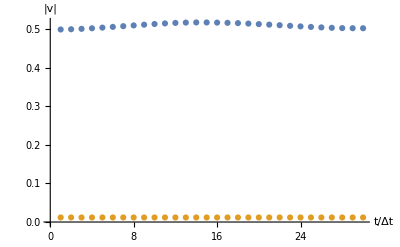

```mathematica
electronsMeanV=Mean[Abs[Last[Transpose[#]]]]&/@electronsList;
ionsMeanV=Mean[Abs[Last[Transpose[#]]]]&/@ionsList;
ListPlot[{electronsMeanV,ionsMeanV},AxesLabel->{"t/Δt","|v|"}]
```

```mathematica
Manipulate[ListPlot[electronsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Electron Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[electronsList],1}]
```

```mathematica
Manipulate[SmoothPhaseSpacePlot[electronsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Electron Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[electronsList],1}]
```

```mathematica
Manipulate[ListPlot[ionsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Ion Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[ionsList],1}]
```

```mathematica
Manipulate[SmoothPhaseSpacePlot[ionsList[[i]],AxesLabel->{"x","v"},PlotLabel->"Ion Phase Space\nt = "<>ToString[i*PicPar["dt"]]],{i,1,Length[ionsList],1}]
```